```mathematica
Mark6 Disk Performance Results
```

## Introduction

This document describes the individual disk performance results for disks in Mark6 disk packs mk6 + 005, mk6 + 006, mk6 + 007, mk6 + 008, mk6 + 009. The results were measured using the FIO linux benchmarking program.

## External Libraries

```mathematica
Needs["ComputerArithmetic`"];
```

```mathematica
Needs["PlotLegends`"];
```

## Import Data

```mathematica
SetDirectory["/opt/src/mark6/tests"];
nrDirectories={"mk6+006","mk6+007","mk6+008"};
(* mk6006, mk6007, mk6008 *)
nrFiles=FileNames[#<>"/disk*.log"]&/@nrDirectories

windowSize=120;
rawData=Function[files,
Function[file,
data=Import[file,"CSV"][[All,{1,2}]];
time=data[[All,1]]/1000;
averageData=MovingAverage[8/1000 data[[All,2]],windowSize];
Partition[Riffle[time,averageData],2]
]/@files
]/@nrFiles;

mk6006Data=rawData[[1]];
Length[mk6006Data]

mk6007Data=rawData[[2]];
Length[mk6007Data]

mk6008Data=rawData[[3]];
Length[mk6008Data]
```

{{mk6+006/disk0_write_bw.log,mk6+006/disk1_write_bw.log,mk6+006/disk2_write_bw.log,mk6+006/disk3_write_bw.log,mk6+006/disk4_write_bw.log,mk6+006/disk5_write_bw.log,mk6+006/disk6_write_bw.log,mk6+006/disk7_write_bw.log},{mk6+007/disk0_write_bw.log,mk6+007/disk1_write_bw.log,mk6+007/disk2_write_bw.log,mk6+007/disk3_write_bw.log,mk6+007/disk4_write_bw.log,mk6+007/disk5_write_bw.log,mk6+007/disk6_write_bw.log,mk6+007/disk7_write_bw.log},{mk6+008/disk0_write_bw.log,mk6+008/disk1_write_bw.log,mk6+008/disk2_write_bw.log,mk6+008/disk3_write_bw.log,mk6+008/disk4_write_bw.log,mk6+008/disk5_write_bw.log,mk6+008/disk6_write_bw.log,mk6+008/disk7_write_bw.log}}

8

8

8

```mathematica
mk6006Data[[1,-200]]//N
```

{9621.91,668.296}

```mathematica
mk6006Data[[1,-200;;-1]]//N
```

{{9621.91,668.296},{9622.41,669.863},{9622.92,668.271},{9623.53,666.197},{9624.17,671.685},{9624.7,667.465},{9625.27,667.873},{9625.77,668.534},{9626.27,667.889},{9626.77,665.111},{9627.34,664.018},{9628.07,664.605},{9628.79,661.345},{9629.29,677.145},{9629.83,672.242},{9630.33,674.935},{9630.83,672.521},{9631.6,669.84},{9632.1,671.707},{9632.75,668.789},{9633.5,670.699},{9634.,668.848},{9634.53,664.148},{9635.04,662.546},{9635.55,660.},{9636.1,658.589},{9636.61,659.169},{9637.11,655.631},{9637.61,653.855},{9638.12,655.293},{9638.63,655.365},{9639.3,651.285},{9639.81,652.639},{9640.52,650.978},{9641.03,651.688},{9641.53,646.801},{9642.27,646.414},{9642.77,645.295},{9643.27,641.238},{9643.77,640.764},{9644.27,638.643},{9644.77,636.809},{9645.39,635.799},{9645.92,632.916},{9646.42,645.897},{9646.97,642.838},{9647.47,644.412},{9647.97,642.491},{9648.76,638.583},{9649.27,640.052},{9649.98,637.187},{9650.48,638.772},{9650.99,632.346},{9651.5,631.926},{9652.01,633.952},{9652.51,627.075},{9653.01,627.573},{9653.51,625.293},{9654.01,623.761},{9654.71,621.96},{9655.29,624.314},{9655.79,622.147},{9656.29,618.174},{9656.87,616.2},{9657.37,618.693},{9657.89,611.723},{9658.4,613.407},{9658.91,608.201},{9659.5,608.314},{9660.21,607.591},{9660.72,605.683},{9661.29,601.882},{9661.8,601.246},{9662.62,596.713},{9663.12,597.754},{9663.62,594.336},{9664.13,594.757},{9664.86,593.149},{9665.36,594.795},{9666.11,591.033},{9666.72,592.64},{9667.22,593.598},{9668.06,1175.17},{9668.56,1107.16},{9669.07,1040.57},{9669.78,971.608},{9670.28,901.084},{9670.79,836.944},{9671.3,801.754},{9671.8,779.248},{9672.67,768.777},{9673.18,775.155},{9673.68,778.057},{9674.42,782.712},{9675.1,785.389},{9675.6,789.644},{9676.35,794.975},{9676.85,801.178},{9677.48,805.977},{9677.98,813.382},{9678.48,815.99},{9678.98,821.767},{9679.49,825.845},{9680.,827.514},{9680.5,833.12},{9681.07,837.909},{9681.58,840.672},{9682.08,844.598},{9682.66,846.928},{9683.32,849.81},{9683.88,851.607},{9684.38,856.718},{9684.99,857.946},{9685.49,862.342},{9685.99,863.475},{9686.85,867.072},{9687.35,869.263},{9687.86,870.885},{9688.36,872.49},{9689.21,875.606},{9689.72,876.602},{9690.4,879.818},{9691.04,881.683},{9691.54,882.218},{9692.21,884.007},{9692.71,887.793},{9693.37,889.474},{9693.93,891.006},{9694.63,893.504},{9695.24,896.843},{9695.74,899.012},{9698.11,902.1},{9698.61,905.2},{9699.11,907.961},{9699.61,908.46},{9700.11,911.575},{9700.86,911.053},{9701.39,912.552},{9701.93,914.438},{9702.68,915.372},{9703.37,915.388},{9703.91,919.12},{9704.51,920.484},{9705.02,919.615},{9705.81,920.265},{9706.73,922.456},{9707.23,923.867},{9707.73,925.888},{9708.23,926.246},{9708.74,927.835},{9709.41,927.445},{9710.,928.416},{9710.5,930.145},{9711.,931.421},{9711.56,933.751},{9712.08,935.613},{9712.6,935.133},{9713.35,935.538},{9713.85,936.271},{9714.63,936.972},{9715.18,939.268},{9715.73,941.019},{9717.79,944.285},{9718.29,946.649},{9718.93,947.154},{9719.44,949.606},{9719.97,949.149},{9720.77,948.748},{9721.46,948.287},{9721.98,949.252},{9722.49,949.129},{9723.03,953.259},{9723.54,954.918},{9724.04,955.158},{9724.56,953.789},{9725.09,954.34},{9725.62,953.794},{9726.12,955.061},{9726.75,956.318},{9727.25,957.241},{9727.77,960.44},{9728.28,960.446},{9728.81,961.194},{9729.31,959.749},{9729.83,960.087},{9730.36,959.317},{9730.99,959.425},{9731.5,960.497},{9732.04,961.134},{9732.6,964.102},{9733.1,966.19},{9733.71,966.871},{9734.26,967.463},{9734.78,967.134},{9735.28,966.401},{9735.78,965.809},{9736.38,967.033},{9736.98,968.004},{9737.52,969.6},{9738.02,971.117}}

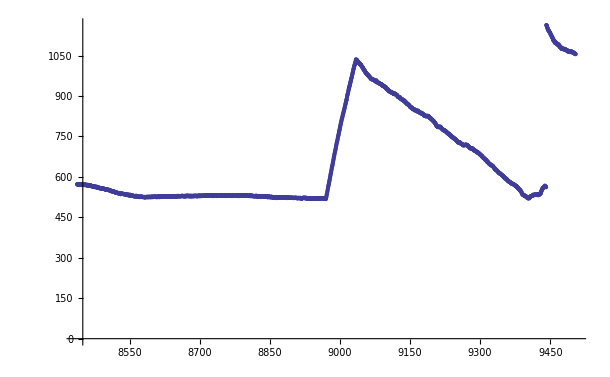

```mathematica
ListPlot[mk6006Data[[7,-2000;;-1]]]
```

```mathematica
mk6007Serials={
"WD-WCATR5882337",
"WD-WCATR5842519",
"WD-WCATR5842024",
"WD-WCATR5854063",
"WD-WCATR5842518",
"WD-WCATR5873146",
"WD-WCATR5854139",
"WD-WCATR5873160"
};

mk6008Serials={
"WD-WCATR5862117",
	"WD-WCATR5836481",
	"WD-WCATR5861698",
	"WD-WCATR5841686",
	"WD-WCATR5861912",
	"WD-WCATR5882097",
	"WD-WCATR5879679",
	"WD-WCATR5879319"
};

mk6005Serials={
	"WD-WCATR5882572",
	"WD-WCATR5862262",
	"WD-WCATR5861552",
	"WD-WCATR5879674",
	"WD-WCATR5873892",
	"WD-WCATR5861375",
	"WD-WCATR5879596",
	"WD-WCATR5884830"
};

mk6006Serials={
"WD-WCATR5861771",
"WD-WCATR5862741",
"WD-WCATR5880404",
"WD-WCATR5880028",
"WD-WCATR5870986",
"WD-WCATR5882830",
"WD-WCATR5880218",
"WD-WCATR5870859"
};
mk6009Serials={
"WD-WMAY01837808",
"WD-WMAY02074904",
"WD-WMAY02074917",
"WD-WMAY01790329",
"WD-WMAY02074892",
"WD-WMAY01548353",
"WD-WMAY02041851",
"WD-WMAY01299169"
};
```

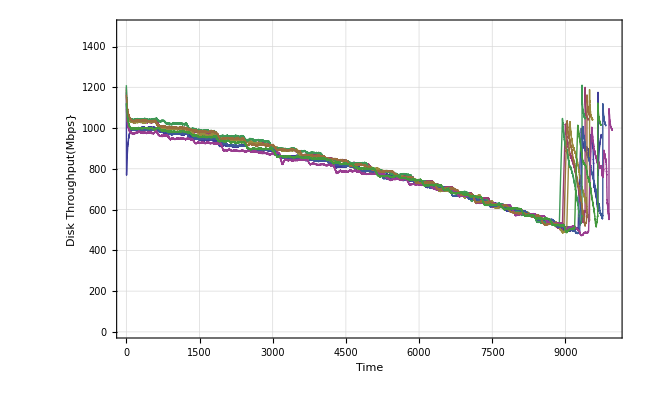

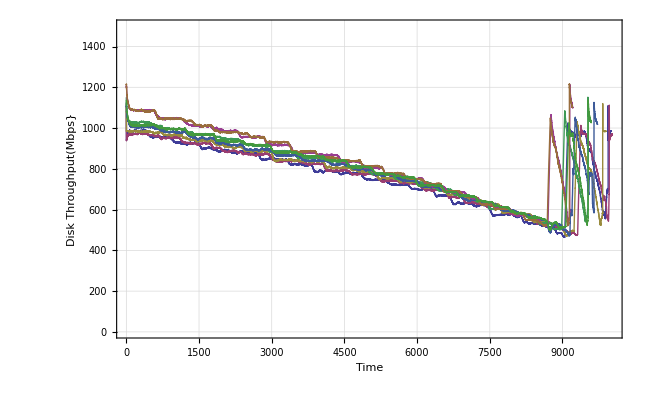

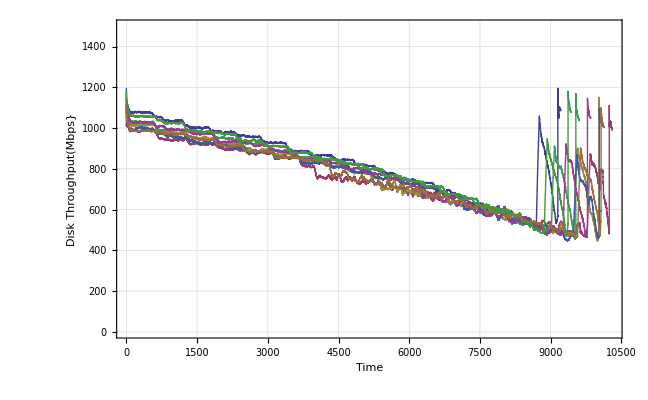

```mathematica
ListPlot[mk6006Data,{Joined->True,PlotRange->{All,{0,1500}},ImageSize->{72 9, 72 6},Frame->True,FrameLabel->{"Time", "Disk Throughput(Mbps}", " Individual Disk Throughput",""},GridLines->Automatic ,PlotLegend->mk6006Serials,LegendShadow->False,LegendPosition->{1.1,-0.4},LegendSize->{0.9,0.8}}]
ListPlot[mk6007Data,{Joined->True,PlotRange->{All,{0,1500}},ImageSize->{72 9, 72 6},Frame->True,FrameLabel->{"Time", "Disk Throughput(Mbps}", " Individual Disk Throughput",""},GridLines->Automatic ,PlotLegend->mk6007Serials,LegendShadow->False,LegendPosition->{1.1,-0.4},LegendSize->{0.9,0.8}}]
ListPlot[mk6008Data,{Joined->True,PlotRange->{All,{0,1500}},ImageSize->{72 9, 72 6},Frame->True,FrameLabel->{"Time", "Disk Throughput(Mbps}", " Individual Disk Throughput",""},GridLines->Automatic ,PlotLegend->mk6008Serials,LegendShadow->False,LegendPosition->{1.1,-0.4},LegendSize->{0.9,0.8}}]
```